#### 1)

```mathematica
f=1/x-2/(√x);
g=2^x/ArcTan[x];
h=x^4 Exp[Sin[x]];
D[f,x]
D[g,x]//Together
D[h,x]//Simplify
```

-1/x^2+1/x^(3/2)

(2^x (-1+ArcTan[x] Log[2]+x^2 ArcTan[x] Log[2]))/((1+x^2) ArcTan[x]^2)

ⅇ^Sin[x] x^3 (4+x Cos[x])

#### 2)

48 x+12 x^2-8 x^3-3 x^4

48+24 x-24 x^2-12 x^3

{{x→-2},{x→-√2},{x→√2}}

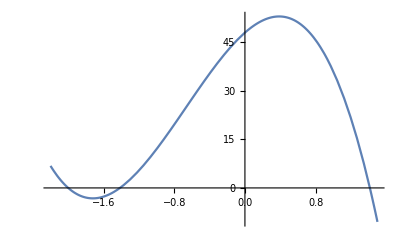

-3 x^4-8 x^3+12 x^2+48 x

```mathematica
(x+2)(2-x^2)//Expand;
Integrate[%,x]12//Expand
%//TeXForm
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-2.2,1.5}]
```

#### 3)

```mathematica
1/(2-I)+(3I)/(1+2I)
(z-3+2I)(z-3-2I)//Expand
```

8/5+(4 ⅈ)/5

13-6 z+z^2

#### 4)

```mathematica
1/(x-1)+2/(x-3)//Together;
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
%%//TeXForm
```

(-5+3 x)/(3-4 x+x^2)

Log[1-x]+2 Log[3-x]

\frac{3 x-5}{x^2-4 x+3}

#### 5)

2-3 x+x^2

{{x→1},{x→2}}

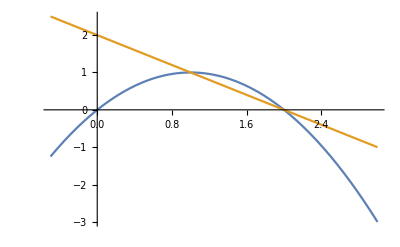

1/6

```mathematica
(x-1)(x-2)//Expand
y1=2x-x^2;
y2=2-x;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-0.5,3}]
Integrate[y1-y2,{x,1,2}]
```

#### 6)

```mathematica
A1={{1,2,1},{2,1,2},{2,2,1}};
Det[A1]
X1={{2},{-4},{3}};
B1=A1.X1
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
```

3

{{-3},{6},{-1}}

{{x→2,y→-4,z→3}}

#### 7)

3-2 x

-1

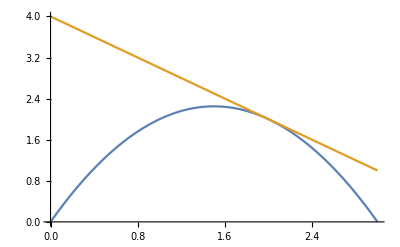

4-x

```mathematica
f1[x_]:=3x-x^2;
f1'[x]
x0=2;
f1'[x0]
g1[x_]:=f1'[x0](x-x0)+f1[x0];
Plot[{f1[x],g1[x]},{x,0,3}]
g1[x]//Expand
```

#### 8)

Dane sa wektory u i v. Wyznacz kosinus kata miedzy nimi oraz pole trojkata rozpietego...

```mathematica
u1={-3,2,6};
v1={3,6,-6};
Dot[u1,v1]/(Norm[u1]Norm[v1])
Cross[u1,v1]
Norm[%]/2
```

-11/21

{-48,0,-24}

12 √5